# Compilation by parts to find a short parameterised SWAP

## Some modules

```mathematica
CountGates::usage="CountGates[circuit], return the count for {doubles, singles}";
CountGates[circuit_]:=Module[{doubles},
doubles=Count[circuit/.{Subscript[C, _][_]->2,Subscript[_, _]-> 1,Subscript[_, _][_]->1},2];
{doubles,Length@circuit-doubles}
]
```

```mathematica
ClearAll[roundingAnsatzSoft]
roundingAnsatzSoft::usage="roundingAnsatzSoft[conf,circ,ansatz,θvars,fraction_of_π,decimal,θerr]. Rounding to multiplication of fraction if rounding difference is less than θerr, otherwise rounded to dec decimals.";
roundingAnsatzSoft[conf_,circ_,ansatz_,θvars_,fraction_,decimal_,θerr_]:=Module[
{idx=0,newkeys,ansatznew,θvarsnew,newcost,cost,roundθ,ψ,ψinit}
,
{ψ,ψinit}=CreateQuregs[conf["nqubit"],2];
PrepareInitState[conf,ψinit];
ApplyCircuit[CloneQureg[ψ,ψinit],circ];
ApplyCircuit[ψ,ansatz/.θvars/.CustomGatesDefinitions];
cost=CostFidelity[ψ,ψinit]; 

newkeys=Table[k->Subscript[θ, idx++],{k,Keys@θvars}];
ansatznew=ansatz/.newkeys;

θvarsnew=<|Table[  
roundθ=Round[θvars[k] ,π/fraction] ;
(k/.newkeys)->If[Abs[roundθ-θvars[k]]<=θerr,roundθ,Round[θvars[k],N[1.0*10^-decimal]]] 
,{k,Keys@θvars}] 
|>;

ApplyCircuit[CloneQureg[ψ,ψinit],circ];
ApplyCircuit[ψ,ansatznew/.θvarsnew/.CustomGatesDefinitions];
newcost=CostFidelity[ψ,ψinit]; 
DestroyQureg[ψ];
DestroyQureg[ψinit];
{ansatznew/.θvarsnew,newcost}
]
```

The parameterised swap

```mathematica
CalcCircuitMatrix[Subscript[SW, 0,1][θ]/.CustomGatesDefinitions]//MatrixForm
CalcCircuitMatrix[Subscript[SW, 0,1][θ]/.CustomGatesDefinitions]//ExpToTrig//TrigReduce//MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^((ⅈ θ)/2) Cos[θ/2] | -ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2] | 0
0 | -ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2] | ⅇ^((ⅈ θ)/2) Cos[θ/2] | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 0
0 | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 0
0 | 0 | 0 | 1)

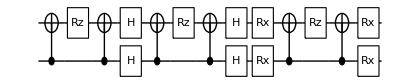

(1 | 0 | 0 | 0
0 | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 0
0 | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 0
0 | 0 | 0 | 1)

```mathematica
sw={Subscript[C, 0][Subscript[X, 1]],Subscript[Rz, 1][θ/2],Subscript[C, 0][Subscript[X, 1]],Subscript[H, 1],Subscript[H, 0],Subscript[C, 0][Subscript[X, 1]],Subscript[Rz, 1][θ/2],Subscript[C, 0][Subscript[X, 1]],Subscript[H, 0],Subscript[H, 1],Subscript[Rx, 0][-π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[X, 1]],Subscript[Rz, 1][θ/2],Subscript[C, 0][Subscript[X, 1]],Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2]};
DrawCircuit[sw]
MatrixForm[TrigReduce[ComplexExpand[ⅇ^(ⅈ θ/4)Simplify[CalcCircuitMatrix[sw/.CustomGatesDefinitions],Reals[θ]]]]]
```

```mathematica
circ={Subscript[C, 0][Subscript[X, 1]],Subscript[H, 0],Subscript[H, 1],Subscript[C, 0][Subscript[X, 1]]};
CalcCircuitMatrix[circ]//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2
1/2 | -1/2 | 1/2 | -1/2)

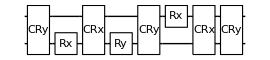
-Graphics-84.9366×10^-10π

Cycle 1@Thu 22 Dec 2022 22:57:50 completed with ngates=6, cost=0.1464466226300456, at eval=1090

Cycle 2@Thu 22 Dec 2022 22:58:05 completed with ngates=7, cost=1.1757671614098797e-8, at eval=1877

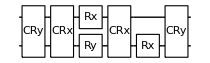
-Graphics-73.36356×10^-9 π/2

Cycle 1@Thu 22 Dec 2022 22:58:35 completed with ngates=4, cost=0.06698729812484094, at eval=1064

Cycle 2@Thu 22 Dec 2022 22:58:44 adjust hyperparams, slowdown:True

Cycle 3@Thu 22 Dec 2022 22:59:08 completed with ngates=7, cost=1.1263034005448702e-7, at eval=2614

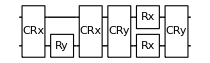
-Graphics-73.36609×10^-10 π/3

Cycle 1@Thu 22 Dec 2022 22:59:28 completed with ngates=9, cost=5.725840838133323e-7, at eval=1041

@cycle2, pathetic result.

Cycle 2@Thu 22 Dec 2022 22:59:44 adjust hyperparams, slowdown:True

Cycle 3@Thu 22 Dec 2022 23:00:12 adjust hyperparams, slowdown:True

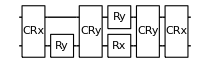
-Graphics-75.20283×10^-9 π/4

Cycle 1@Thu 22 Dec 2022 23:00:32 completed with ngates=6, cost=0.024471756885966034, at eval=1124

Cycle 2@Thu 22 Dec 2022 23:00:46 completed with ngates=7, cost=3.5489937122434867e-7, at eval=1943

@cycle3, pathetic result.

Cycle 3@Thu 22 Dec 2022 23:00:57 adjust hyperparams, slowdown:True

Cycle 4@Thu 22 Dec 2022 23:01:18 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-8; cost=6.85269×10^-8

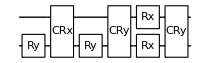
-Graphics-72.14214×10^-8 π/5

Cycle 1@Thu 22 Dec 2022 23:01:33 completed with ngates=8, cost=1.9920547311702563e-7, at eval=1069

Cycle 2@Thu 22 Dec 2022 23:01:49 adjust hyperparams, slowdown:True

Cycle 3@Thu 22 Dec 2022 23:02:16 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-8; cost=1.17197×10^-7

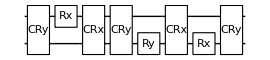
-Graphics-84.34632×10^-8 π/6

Cycle 1@Thu 22 Dec 2022 23:02:37 completed with ngates=8, cost=0.012536159904105837, at eval=1081

Cycle 2@Thu 22 Dec 2022 23:02:55 completed with ngates=10, cost=0.00044458498060706564, at eval=1883

Cycle 3@Thu 22 Dec 2022 23:03:13 adjust hyperparams, slowdown:True

Cycle 4@Thu 22 Dec 2022 23:03:42 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-8; cost=5.56717×10^-7

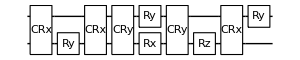
-Graphics-102.7357×10^-7 π/7

Cycle 1@Thu 22 Dec 2022 23:04:04 completed with ngates=7, cost=0.009628959173256346, at eval=1051

Cycle 2@Thu 22 Dec 2022 23:04:20 completed with ngates=9, cost=0.0007779071652197489, at eval=1785

Cycle 3@Thu 22 Dec 2022 23:04:40 completed with ngates=9, cost=4.618693405511465e-8, at eval=2598

Cycle 4@Thu 22 Dec 2022 23:04:56 adjust hyperparams, slowdown:True

Cycle 5@Thu 22 Dec 2022 23:05:24 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-8; cost=4.57217×10^-8

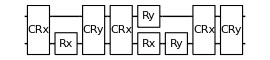
-Graphics-91.15704×10^-8 π/8

Cycle 1@Thu 22 Dec 2022 23:05:43 completed with ngates=4, cost=0.007596865647072182, at eval=1016

Cycle 2@Thu 22 Dec 2022 23:05:54 completed with ngates=4, cost=0.0075961251162465215, at eval=1704

@cycle3, pathetic result.

Cycle 3@Thu 22 Dec 2022 23:06:06 adjust hyperparams, slowdown:True

Cycle 4@Thu 22 Dec 2022 23:06:31 completed with ngates=7, cost=0.000011624869294957207, at eval=3203

Cycle 5@Thu 22 Dec 2022 23:07:01 completed with ngates=13, cost=1.9440129728209854e-8, at eval=4219

Cycle 6@Thu 22 Dec 2022 23:07:50 adjust hyperparams, slowdown:True

Cycle 7@Thu 22 Dec 2022 23:09:12 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-8; cost=1.94401×10^-8

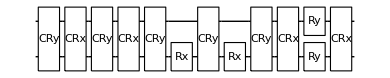
-Graphics-131.94401×10^-8 π/9

Cycle 1@Thu 22 Dec 2022 23:09:35 completed with ngates=8, cost=0.00615583918827356, at eval=1065

Cycle 2@Thu 22 Dec 2022 23:09:51 adjust hyperparams, slowdown:True

Cycle 3@Thu 22 Dec 2022 23:10:21 completed with ngates=8, cost=2.794019904328593e-9, at eval=2595

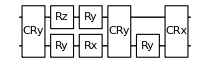
-Graphics-82.79402×10^-9 π/10

```mathematica
DestroyAllQuregs[]
j=1;
results=Table[
conf=DefaultConfig[2,{0,1,2,3}];
θ=π/j++;
mat=CalcCircuitMatrix[{Subscript[SW, 0,1][θ]/.CustomGatesDefinitions}];
res=CJRecompile[2,mat,conf];
{ansatz,θvars}=res[[4;;5]];
Print[DrawCircuit[ansatz,2],Length@ansatz,res[[2]],θ];
{θ,ansatz,θvars,res[[2]]}
,{10}];
```

```mathematica
results[[1]]
```

{π,{CRy_(0,1)[π_1],Rx_0[π_2],CRx_(0,1)[π_3],Ry_0[π_4],CRy_(0,1)[π_5],Rx_1[π_6],CRx_(0,1)[π_9],CRy_(0,1)[π_10]},<|π_1→1.5708,π_2→1.5708,π_3→-1.5708,π_4→1.5708,π_5→-3.14159,π_6→-4.71243,π_9→-1.5708,π_10→1.57079|>,4.9366×10^-10}

```mathematica
accuracy=10^-2;
fraction=10;
decimal=10;
Table[
{θ,ansatz,θvars,cost}=res;
{circ,cost}=roundingAnsatzSoft[conf,Subscript[SW, 0,1][θ]/.CustomGatesDefinitions,ansatz,θvars,decimal,fraction,accuracy];
Print[θ,circ,cost]
,{res,results}]
```

π{CRy_(0,1)[π/2],Rx_0[π/2],CRx_(0,1)[-π/2],Ry_0[π/2],CRy_(0,1)[-π],Rx_1[-(3 π)/2],CRx_(0,1)[-π/2],CRy_(0,1)[π/2]}6.66134×10^-16

π/2{CRy_(0,1)[-(3 π)/2],CRx_(0,1)[π/2],Rx_1[-0.785398],Ry_0[-0.785396],CRx_(0,1)[-π/2],Rx_0[0.785398],CRy_(0,1)[-π/2]}8.51763×10^-13

π/3{CRx_(0,1)[π/2],Ry_0[-0.523625],CRx_(0,1)[-π/2],CRy_(0,1)[π/2],Rx_1[-0.523599],Rx_0[0.523599],CRy_(0,1)[(3 π)/2]}1.77509×10^-10

π/4{CRx_(0,1)[-π/2],Ry_0[-2.74889],CRy_(0,1)[-π/2],Ry_1[-3.53429],Rx_0[-3.53416],CRy_(0,1)[π/2],CRx_(0,1)[π/2]}4.40391×10^-9

π/5{Ry_0[-π/2],CRx_(0,1)[-π/10],Ry_0[π/2],CRy_(0,1)[(3 π)/2],Rx_0[-π/10],Rx_1[-(19 π)/10],CRy_(0,1)[π/2]}2.22045×10^-16

π/6{CRy_(0,1)[π/2],Rx_1[-0.261799],CRx_(0,1)[-π/2],CRy_(0,1)[-π],Ry_0[-0.261803],CRx_(0,1)[-π/2],Rx_0[-0.261799],CRy_(0,1)[π/2]}3.31402×10^-12

π/7{CRx_(0,1)[-π/2],Ry_0[0.224428],CRx_(0,1)[1.59954],CRy_(0,1)[-π/2],Rx_0[-0.22436],Ry_1[-4.81968],CRy_(0,1)[-π/2],Rz_0[-π],CRx_(0,1)[0.22573],Ry_1[1.68087]}4.32277×10^-6

π/8{CRx_(0,1)[π/2],Rx_0[-π/2],CRy_(0,1)[0.19635],CRx_(0,1)[-π],Rx_0[π/2],Ry_1[-3.33794],Ry_0[2.94546],CRx_(0,1)[(3 π)/2],CRy_(0,1)[π]}1.14781×10^-8

π/9{CRy_(0,1)[-2.38757],CRx_(0,1)[-2.97284],CRy_(0,1)[-1.35481],CRx_(0,1)[-3.27499],CRy_(0,1)[(3 π)/5],Rx_0[0.0710479],CRy_(0,1)[1.10235],Rx_0[0.130668],CRy_(0,1)[-1.94426],CRx_(0,1)[-1.38032],Ry_0[0.174533],Ry_1[-0.174546],CRx_(0,1)[π/2]}2.9843×10^-6

π/10{CRy_(0,1)[π/2],Rz_1[π/2],Ry_0[π],Rx_0[-0.15708],Ry_1[-0.15708],CRy_(0,1)[π/2],Ry_0[-2.98452],CRx_(0,1)[π/2]}1.43552×10^-12

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
π/5{Subscript[Ry, 0][-π/2],Subscript[CRx, 0,1][-π/10],Subscript[Ry, 0][π/2],Subscript[CRy, 0,1][(3 π)/2],Subscript[Rx, 0][-π/10],Subscript[Rx, 1][-(19 π)/10],Subscript[CRy, 0,1][π/2]}2.220446049250313*^-16
```

```mathematica
swa[θ_]:={Subscript[Ry, 0][-π/2],Subscript[CRx, 0,1][θ/2],Subscript[Ry, 0][π/2],Subscript[CRy, 0,1][-π/2],Subscript[Rx, 0][θ/2],Subscript[Rx, 1][-θ/2],Subscript[CRy, 0,1][π/2]}
```

```mathematica
MatrixForm[TrigReduce[ComplexExpand[ⅇ^(ⅈ θ/4) Simplify[CalcCircuitMatrix[swa[θ]/.CustomGatesDefinitions],Reals[θ]]]]]
```

(1 | 0 | 0 | 0
0 | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 0
0 | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 0
0 | 0 | 0 | 1)

goal:(1 | 0 | 0 | 0
0 | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 0
0 | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 0
0 | 0 | 0 | 1)

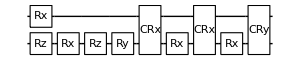

```mathematica
DrawCircuit[ansatz,2]
```

```mathematica
CalcCircuitMatrix[ansatz/.θvars/.CustomGatesDefinitions]//MatrixForm
```

(-0.5-0.0000423114 ⅈ | -0.5-0.0000423131 ⅈ | -0.5-0.0000423131 ⅈ | -0.5-0.0000423114 ⅈ
-0.5+0.0000423131 ⅈ | -0.5+0.0000423114 ⅈ | 0.5-0.0000423114 ⅈ | 0.5-0.0000423131 ⅈ
-0.5+0.0000423131 ⅈ | 0.5-0.0000423114 ⅈ | 0.5-0.0000423114 ⅈ | -0.5+0.0000423131 ⅈ
-0.5-0.0000423114 ⅈ | 0.5+0.0000423131 ⅈ | -0.5-0.0000423131 ⅈ | 0.5+0.0000423114 ⅈ)

{Rx_0[θ_7],Rx_0[θ_13],CRx_(0,1)[θ_16],CRy_(0,1)[θ_17],Rz_0[θ_18],CRx_(0,1)[θ_19],CRy_(0,1)[θ_20],CRx_(0,1)[θ_21]}

For SQC case

```mathematica
ClearAll[θ]
```

```mathematica
mat//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

Cycle 1@Thu 16 Feb 2023 20:45:59 completed with ngates=6, cost=0.5, at eval=1811

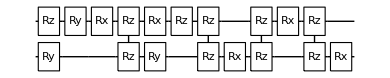
-Graphics-144.87841×10^-11

Cycle 1@Thu 16 Feb 2023 20:46:11 completed with ngates=12, cost=2.654577235805533e-8, at eval=1748

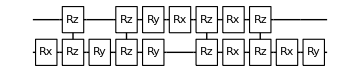
-Graphics-132.82622×10^-9

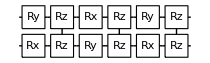
-Graphics-96.1375×10^-10

Cycle 1@Thu 16 Feb 2023 20:46:25 completed with ngates=11, cost=1.6719958750854857e-13, at eval=1745

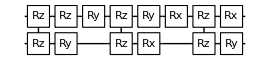
-Graphics-111.672×10^-13

Cycle 1@Thu 16 Feb 2023 20:46:35 completed with ngates=11, cost=1.8456063233251996e-8, at eval=1850

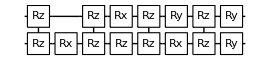
-Graphics-111.30792×10^-10

Cycle 1@Thu 16 Feb 2023 20:46:47 completed with ngates=10, cost=0.500000000459118, at eval=1861

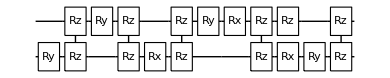
-Graphics-132.96871×10^-9

Cycle 1@Thu 16 Feb 2023 20:47:00 completed with ngates=6, cost=0.4999999999999999, at eval=1592

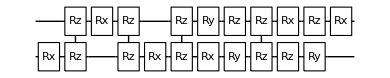
-Graphics-162.84732×10^-9

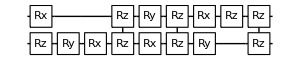
-Graphics-122.22045×10^-16

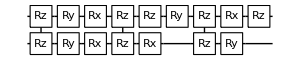
-Graphics-133.85725×10^-11

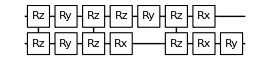
-Graphics-117.92796×10^-9

```mathematica
DestroyAllQuregs[]
j=1;
results=Table[
conf=DefaultConfig[2,{0,1,2,3}];
mat=CalcCircuitMatrix[{Subscript[SWAP, 0,1]}];
res=CJRecompile[2,mat,conf];
{ansatz,θvars}=res[[4;;5]];
Print[DrawCircuit[ansatz,2],Length@ansatz,res[[2]]];
{ansatz,θvars,res[[2]]}
,{10}];
```

```mathematica
accuracy=10^-2;
fraction=10;
decimal=10;
Table[
{ansatz,θvars,cost}=res;
{circ,cost}=roundingAnsatzSoft[conf,Subscript[SWAP, 0,1]/.CustomGatesDefinitions,ansatz,θvars,decimal,fraction,accuracy];
{circ,Length@circ,DrawCircuit[circ],cost}
,{res,results}]
```

{{{Ry_0[π/2],Rz_1[-0.404334],Ry_1[-π/2],Rx_1[-0.404329],R[π/2,Z_0 Z_1],Rx_1[-π/2],Ry_0[-π/2],Rz_1[-π/2],R[π/2,Z_0 Z_1],Rx_0[π/2],R[π/2,Z_0 Z_1],Rx_1[π/2],R[π/2,Z_0 Z_1],Rx_0[π]},14,-Graphics-,4.99811×10^-12},{{Rx_0[-(3 π)/2],R[π/2,Z_0 Z_1],Ry_0[-π/2],R[π/2,Z_0 Z_1],Ry_1[π/2],Ry_0[π],Rx_1[0.121334],R[π/2,Z_0 Z_1],Rx_0[-(5 π)/2],Rx_1[-(5 π)/2],R[π/2,Z_0 Z_1],Rx_0[1.44955],Ry_0[-π/2]},13,-Graphics-,1.99772×10^-9},{{Rx_0[π/2],Ry_1[-π/2],R[π/2,Z_0 Z_1],Ry_0[-π/2],Rx_1[π/2],R[π/2,Z_0 Z_1],Ry_1[-π/2],Rx_0[π/2],R[π/2,Z_0 Z_1]},9,-Graphics-,2.22045×10^-16},{{R[π/2,Z_0 Z_1],Rz_1[-π/2],Ry_0[π/2],Ry_1[π/2],R[π/2,Z_0 Z_1],Ry_1[π/2],Rx_0[-π/2],Rx_1[π/2],R[π/2,Z_0 Z_1],Rx_1[-π/2],Ry_0[π/2]},11,-Graphics-,3.33067×10^-16},{{R[π/2,Z_0 Z_1],Rx_0[π/2],R[π/2,Z_0 Z_1],Rx_1[π/2],Rz_0[-π/2],R[π/2,Z_0 Z_1],Rx_0[π/2],Ry_1[-π/2],R[π/2,Z_0 Z_1],Ry_1[π/2],Ry_0[-π/2]},11,-Graphics-,2.22045×10^-16},{{Ry_0[-π/2],R[π/2,Z_0 Z_1],Ry_1[π/2],R[π/2,Z_0 Z_1],Rx_0[π/2],R[π/2,Z_0 Z_1],Ry_1[0.208201],Rx_1[-π/2],R[π/2,Z_0 Z_1],Rx_0[π/2],Rz_1[0.208221],Ry_0[-(3 π)/2],R[π/2,Z_0 Z_1]},13,-Graphics-,1.02822×10^-10},{{Rx_0[0.92106],R[π/2,Z_0 Z_1],Rx_1[π/2],R[π/2,Z_0 Z_1],Rx_0[π/2],R[π/2,Z_0 Z_1],Rx_0[-π/10],Ry_1[π/2],Ry_0[-π/2],Rz_1[0.388524],R[π/2,Z_0 Z_1],Rz_0[π/10],Rx_1[π/2],Rz_1[-π/2],Ry_0[π/2],Rx_1[-0.532536]},16,-Graphics-,3.33067×10^-16},{{Rz_0[-0.163768],Rx_1[π/2],Ry_0[π/2],Rx_0[0.133193],R[π/2,Z_0 Z_1],Rx_0[π/2],Ry_1[π/2],R[π/2,Z_0 Z_1],Rx_1[π/2],Ry_0[π/2],Rz_1[0.0305758],R[π/2,Z_0 Z_1]},12,-Graphics-,3.33067×10^-16},{{R[π/2,Z_0 Z_1],Ry_0[-π/2],Ry_1[0.134793],Rx_1[-π/2],Rx_0[0.0164489],R[π/2,Z_0 Z_1],Rx_0[-π/2],Rz_1[0.134786],Ry_1[-π/2],R[π/2,Z_0 Z_1],Rx_1[-π/2],Ry_0[-π/2],Rz_1[0.0164414]},13,-Graphics-,2.59128×10^-11},{{R[π/2,Z_0 Z_1],Ry_1[π/2],Ry_0[-π/2],R[π/2,Z_0 Z_1],Rz_1[-π/2],Rx_0[π/2],Ry_1[-π/2],R[π/2,Z_0 Z_1],Rx_0[π/2],Rx_1[π/2],Ry_0[-π/2]},11,-Graphics-,2.22045×10^-16}}

```mathematica
circ={Subscript[Rx, 0][π/2],Subscript[Ry, 1][-π/2],R[π/2,Subscript[Z, 0] Subscript[Z, 1]],Subscript[Ry, 0][-π/2],Subscript[Rx, 1][π/2],R[π/2,Subscript[Z, 0] Subscript[Z, 1]],Subscript[Ry, 1][-π/2],Subscript[Rx, 0][π/2],R[π/2,Subscript[Z, 0] Subscript[Z, 1]]}
```

{Rx_0[π/2],Ry_1[-π/2],R[π/2,Z_0 Z_1],Ry_0[-π/2],Rx_1[π/2],R[π/2,Z_0 Z_1],Ry_1[-π/2],Rx_0[π/2],R[π/2,Z_0 Z_1]}

```mathematica
mat
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

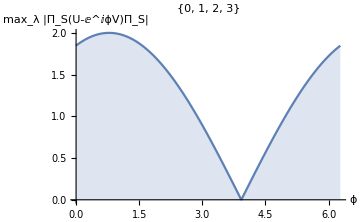
-Graphics-{ϕ→3.92699}

4.12854×10^-16

```mathematica
MatrixDist[CalcCircuitMatrix[circ],mat,{0,1,2,3},True]
```

```mathematica
ExpandAll[-ⅈ *ⅇ^(ⅈ 5π/4)*CalcCircuitMatrix[circ]]
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

```mathematica
N[5 π/4]
```

3.92699